```mathematica
Needs["PlotLegends`"]
```

```mathematica
v="11";
p="0.1";
g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
```

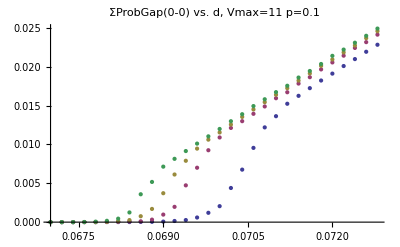

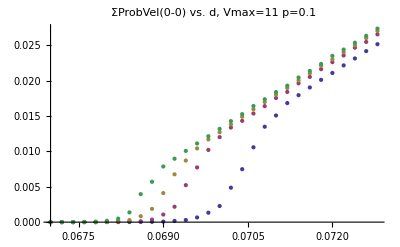

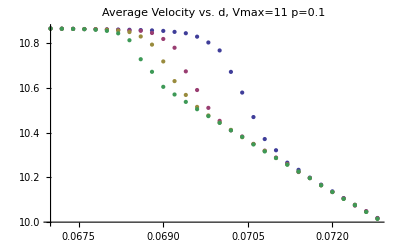

```mathematica
ngap="0";
nvel="0";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v11=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v11=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v5k1]}];
avel5v11=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v11=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v11=Table[{v10k1[[All,1]][[j]],(1-Sum[v10k1[[All,i]][[j]],{i,3,13}])+Sum[v10k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v10k1]}];
avel10v11=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v11=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v11=Table[{v20k1[[All,1]][[j]],(1-Sum[v20k1[[All,i]][[j]],{i,3,13}])+Sum[v20k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v20k1]}];
avel20v11=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v11=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v11=Table[{v30k1[[All,1]][[j]],(1-Sum[v30k1[[All,i]][[j]],{i,3,13}])+Sum[v30k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v30k1]}];
avel30v11=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap50v11=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v11=Table[{v50k1[[All,1]][[j]],(1-Sum[v50k1[[All,i]][[j]],{i,3,13}])+Sum[v50k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v50k1]}];
avel50v11=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];


ListPlot[{gap10v11,gap20v11,gap30v11,gap50v11},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel10v11,vel20v11,vel30v11,vel50v11},PlotLabel->"ΣProbVel(0-"<>nvel<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{avel10v11,avel20v11,avel30v11,avel50v11},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotRange->Full,PlotLegend->{"10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

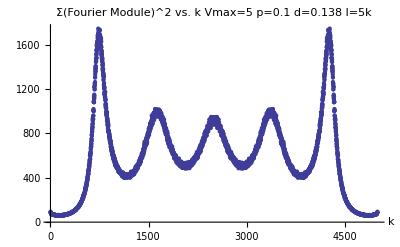

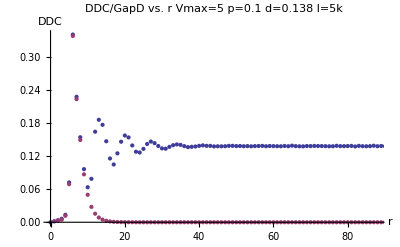

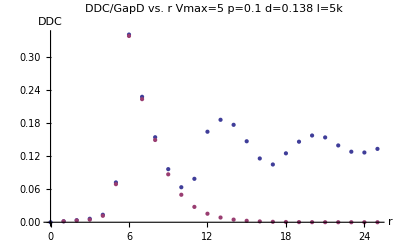

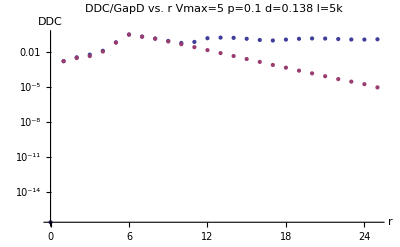

```mathematica
d="0.138";
l="5";
v="5";
p="0.1";
fourier=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Fourier1D-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddc=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/DDC-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
gf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapDFull-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ListPlot[fourier,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,88},Full},PlotLegend->{"DDC","Gap D."},LegendPosition->{1.1,-0.4},LegendSize->{0.4,0.6},LegendShadow->None]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,25},Full}]
ListLogPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,25},Full}]
```

```mathematica
gap1000=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10k1]}];
gap1001=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g10k1]}];
gap1002=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g10k1]}];
gap1003=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g10k1]}];
gap1004=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g10k1]}];
gap1005=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g10k1]}];
gap1006=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,8,8}]},{j,1,Length[g10k1]}];
gap1007=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,9,9}]},{j,1,Length[g10k1]}];
gap1008=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,10,10}]},{j,1,Length[g10k1]}];
gap1009=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,11,11}]},{j,1,Length[g10k1]}];
gap1010=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,12,12}]},{j,1,Length[g10k1]}];
gap1011=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,13,13}]},{j,1,Length[g10k1]}];
```

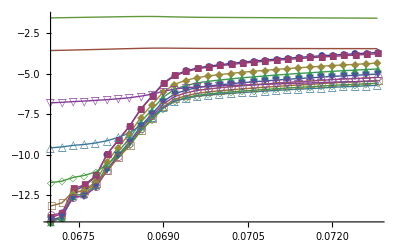

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005,gap1006,gap1007,gap1008,gap1009,gap1010,gap1011},PlotLegend->{"0","1","2","3","4","5","6","7","8","9","10","11"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full,PlotLabel->"GapDistribution, Vmax=11, 30k"]
```